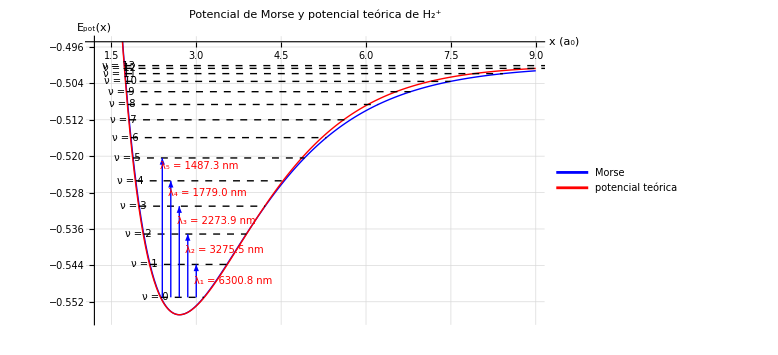

xₘᵢₙ real (a₀) | 2.7036
Eₘᵢₙ real (Eh) | -0.554849
E∞ real (Eh) | -0.500000
Dₑ = EB (Eh) | 0.054849
a (a₀⁻.b9) | 0.712042
ωₑ (Eh) | 0.007784
νₘₐₓ teórico (Morse) | 13
Δ_asíntota (Morse − Real) [Eh] | -4.162605×10^-8

Nivel | E_rel (Eh) | E_abs (Eh)
ν = 0 | 0.003823 | -0.551026
ν = 1 | 0.011054 | -0.543795
ν = 2 | 0.017733 | -0.537115
ν = 3 | 0.023860 | -0.530989
ν = 4 | 0.029434 | -0.525414
ν = 5 | 0.034457 | -0.520392
ν = 6 | 0.038926 | -0.515922
ν = 7 | 0.042844 | -0.512005
ν = 8 | 0.046209 | -0.508639
ν = 9 | 0.049022 | -0.505826
ν = 10 | 0.051283 | -0.503566
ν = 11 | 0.052991 | -0.501857
ν = 12 | 0.054148 | -0.500701
ν = 13 | 0.054751 | -0.500097

```mathematica
(* ===============Limpieza===============*)
ClearAll["Global`*"];

(* ===============Constantes físicas===============*)
hbar=1;
mu=918;
EB=0.0548486;           (*profundidad del Morse,en Eh*)
a=0.712042;             (*parámetro de ancho,a0^-1*)
Xmin=2.70359;           (*posición del mínimo del Morse*)
Za=1;C1=1;
hartreeToNm=45.563;     (*λ[nm] por Hartree de ΔE*)
spacing=0.0034;         (*separador vertical de etiquetas λ*)

(* ===============Potencial “teórica” homogéneo en términos de x===============*)
Ex[x_,Za_,C1_]:=(E^-x Za^2 (6 (1+C1^2) (1+x)-3 (1+C1^2) E^(2 x) (2+x-2 Za)-2 C1 E^x (3+9 x+9 x^2+x^3-2 (6+x (3+x)) Za)))/(2 x (3 (1+C1^2) E^x+2 C1 (3+x (3+x))));

(* ===============Mínimo y asíntota del potencial teórica===============*)
xMinReal=x/. NMinimize[{Ex[x,Za,C1],1<x<9},x][[2]];
EminReal=Ex[xMinReal,Za,C1];
EinfReal=Ex[50.,Za,C1];                 (*aprox asíntota R->∞*)

offset=EminReal;   (*alineamos energéticamente el mínimo*)
(* ===============Potencial de Morse ===============*)
MorseV[x_]:=offset+EB (1-Exp[-a (x-Xmin)])^2;

(* ===============Niveles vibracionales (Morse)===============*)
omega0=a*Sqrt[(2*EB)/mu];                 (*ω_e en unidades atómicas*)
Evib[nu_]:=omega0 (nu+1/2)-(omega0^2 (nu+1/2)^2)/(4*EB);

(*máximo teórico de niveles ligados del Morse*)
nuMaxTheory=Floor[(2*EB)/omega0-1/2];

(*si quieres limitar la gráfica a un número concreto, usa este:*)
maxNu=13;   

(* ===puntos de giro del nivel ν resolviendo V_Morse(x)=Eν+offset===*)
intersectionPoints[Elevel_]:=Module[{sols},sols=x/. NSolve[MorseV[x]==(Elevel+offset)&&x>0,x,Reals];
If[Length[sols]>=2,{Min[sols],Max[sols]},{}]];

(* ===============Gráfica base:Morse y teórica juntos===============*)
plotRangeY={offset-0.001,offset+0.06};  
xRange={1.2,9};

basePlot=Plot[{MorseV[x],Ex[x,Za,C1]},{x,Sequence@@xRange},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->{plotRangeY},AxesLabel->{"x (a_0)","E_pot(x)"},PlotLegends->{"Morse","potencial teórica"},GridLines->Automatic,PlotLabel->"Potencial de Morse y potencial teórica de H_2^+",ImageSize->Large,PlotPoints->200];

(* ===============Líneas de niveles (segmentos entre puntos de giro)===============*)
levelLines=Graphics@Table[Module[{E=Evib[nu],r12},r12=intersectionPoints[E];
If[r12==={},Nothing,{{Dashed,Black,Line[{{r12[[1]],E+offset},{r12[[2]],E+offset}}]},Text[Style["ν = "<>ToString[nu],10],{r12[[1]]-0.1,E+offset},{1,0}]}]],{nu,0,maxNu}];

(* ===============Flechas de transición desde v=0 con λ en nm===============*)
transitionArrows=Graphics@Table[Module[{E1=Evib[0]+offset,E2=Evib[v]+offset,mid,xBase,lam},xBase=3-0.15 (v-1);(*escalonado a la izquierda,como el tuyo*)mid=(E1+E2)/2;
lam=hartreeToNm/(E2-E1);
{Blue,Arrow[{{xBase,E1},{xBase,E2}}],Text[Style[Row[{Subscript["λ",v]," = ",NumberForm[lam,{6,1}]," nm"}],10,Red],{xBase+0.65,mid+spacing (v-1)},{0,0}]}],{v,1,5}];

Show[basePlot,levelLines,transitionArrows]

(* =====================TABLA 1:Parámetros usados=====================*)
deltaAsym=(offset+EB)-EinfReal;  (*Morse-Real en la asíntota*)

paramTable=Grid[{{"xₘᵢₙ real (a₀)",NumberForm[xMinReal,{6,4}]},{"Eₘᵢₙ real (Eh)",NumberForm[EminReal,{8,6}]},{"E∞ real (Eh)",NumberForm[EinfReal,{8,6}]},{"Dₑ = EB (Eh)",NumberForm[EB,{8,6}]},{"a (a₀⁻.b9)",NumberForm[a,{8,6}]},{"ωₑ (Eh)",NumberForm[omega0,{8,6}]},{"νₘₐₓ teórico (Morse)",nuMaxTheory},{"Δ_asíntota (Morse − Real) [Eh]",NumberForm[deltaAsym,{8,6}]}},Frame->All,Spacings->{2,1}];

paramTable

(* =====================TABLA 2:Niveles vibracionales=====================*)
(*desde v=0 hasta el máximo teórico del Morse*)
energyTable=Table[{"ν = "<>ToString[nu],NumberForm[Evib[nu],{8,6}],(*energía relativa al fondo*)NumberForm[EminReal+Evib[nu],{8,6}]    (*energía absoluta*)},{nu,0,nuMaxTheory}];

TableForm[energyTable,TableHeadings->{None,{"Nivel","E_rel (Eh)","E_abs (Eh)"}}]
```

#### Notas

Es la energía relativa al mínimo del potencial, medida en unidades atómicas (Hartree). Matemáticamente corresponde al valor  que entrega la fórmula de niveles vibracionales: , i.e., es cuánto “por arriba del fondo” del pozo está colocado ese nivel vibracional. E.g. si el nivel base  aparece con , significa que el estado fundamental está a esa altura sobre el fondo del pozo de Morse.

es la energía absoluta total, también en Hartree, pero ahora incluyendo la posición del mínimo real del potencial. ():

Esta es la cantidad que se puede comparar directamente con la curva de potencial “real” .
Es decir, si dibujas la curva roja (potencial real) y colocas estas líneas horizontal en , coinciden con los niveles de energía física del sistema.

#### Resumen

lo que predice el modelo del oscilador  de Morse para cada , medido desde el fondo.
 la posición real del nivel dentro de la curva completa del potencial, listo para compararse con la gráfica roja

#### Comentarios:

En otra libreta aparte repetí este código pero usando la función heterogénea Etot y obtuve esto para Za=0.9999, Zb=1:

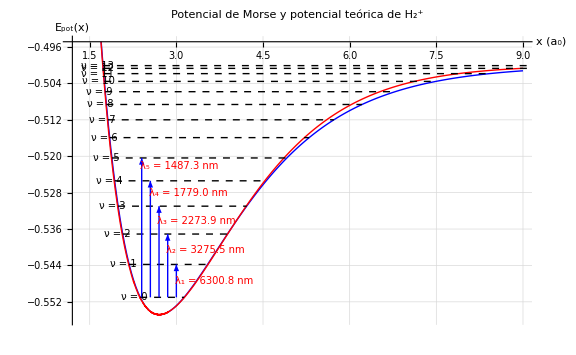

xₘᵢₙ real (a₀) | 2.7032
Eₘᵢₙ real (Eh) | -0.554833
E∞ real (Eh) | -0.499951
Dₑ = EB (Eh) | 0.054849
a (a₀⁻.b9) | 0.712042
ωₑ (Eh) | 0.007784
νₘₐₓ teórico (Morse) | 13
Δ_asíntota (Morse − Real) [Eh] | -0.000033

Nivel | E_rel (Eh) | E_abs (Eh)
ν = 0 | 0.003823 | -0.551010
ν = 1 | 0.011054 | -0.543779
ν = 2 | 0.017733 | -0.537100
ν = 3 | 0.023860 | -0.530973
ν = 4 | 0.029434 | -0.525399
ν = 5 | 0.034457 | -0.520376
ν = 6 | 0.038926 | -0.515907
ν = 7 | 0.042844 | -0.511989
ν = 8 | 0.046209 | -0.508624
ν = 9 | 0.049022 | -0.505811
ν = 10 | 0.051283 | -0.503550
ν = 11 | 0.052991 | -0.501842
ν = 12 | 0.054148 | -0.500685
ν = 13 | 0.054751 | -0.500082